#### Problem description

```mathematica
Import["/Users/wenqiangfang/Dropbox (Brown)/Apps/OverLeafGit/StairStep/Figures/BeamSchematic_V10.png"]
```

-Graphics-

The governing equation for the Euler Elastica problem is

E I (d^2 θ)/(d s^2)+P_1 sin(θ)- P_2 cos(θ)=0

where 0≤s≤S is the arc length coordinate, θ is the angle of deflection (in radians) at point s, P_1 (positive when pointing to right) and P_2 (positive when pointing downward) are the horizontal and vertical forces at the left end of the beam, respectively.

We define θ as the angle from (ê)_1 to T̂ in the counter clockwise direction. (counter clockwise direction is the direction from (ê)_1 to (ê)_2.) We should have cos(θ) =T̂·(ê)_1

r(s)=x_1(s)(ê)_1+x_2(s) (ê)_2
T = (d r(s))/(d s)=x_1'(s)(ê)_1+x_2'(s) (ê)_2
||T||=√((x_1')^2+(x_2')^2)=1 (inextensibility)
T̂ =T/||T||=T
T̂·(ê)_1=x_1'(s)=cos(θ(s))
x_2'=sin(θ(s))
T=cos(θ(s))(ê)_1+sin(θ(s))(ê)_2
N=(d T(s))/(d s)=x_1''(s)(ê)_1+x_2''(s) (ê)_2
x_1''(s)=-sin(θ(s))θ'(s)
x_2''(s)=cos(θ(s))θ'(s)
||N|| = √((x_1'')^2+(x_2'')^2)=√((θ'(s))^2)=|θ'(s)| 
N̂=N/||N||=sign(θ'(s))(-sin(θ(s))(ê)_1+cos(θ(s)) (ê)_2)

The external force is P=P_1(ê)_1+P_2(ê)_2=P_n N̂-P_t T̂ and P_t=μ P_n.
In this case sign(θ'(s)) = -1, N̂=sin(θ(s))(ê)_1-cos(θ(s)) (ê)_2

P_1=P_n sin(θ_0)-μ P_n cos(θ_0)
P_2=-(P_n cos(θ_0)+μ P_n sin(θ_0))

Let ξ=2s/S, θ̂(ξ)=θ(s),  k=(P_n S^2)/(4 E I), g(ξ)=θ̂(ξ)-OverHat[θ_0]then the equation becomes

E I (d^2 θ)/(d s^2)+P_n(sin(θ_0)-μ  cos(θ_0))sin(θ)-P_n( cos(θ_0)+μ  sin(θ_0))cos(θ)=0
E I (d^2 θ)/(d s^2)-P_n(-cos(θ-θ_0)+μ  sin(θ-θ_0))=0
(d^2 θ̂(ξ))/(d ξ^2)=S^2/4(d^2 θ)/(d s^2)
(d^2 θ̂(ξ))/(d ξ^2)+k (cos(θ̂-OverHat[θ_0])-μ  sin(θ̂-OverHat[θ_0]))=0
(d^2 g(ξ))/(d ξ^2)+k (cos(g(ξ))-μ  sin(g(ξ)))=0

The simplified governing equation and boundary conditions are as follows

(d^2 g(ξ))/(d ξ^2)+k (cos(g(ξ))-μ  sin(g(ξ)))=0
g(ξ=0)=0
g'(ξ=0)=0
g(ξ=1)=-θ_0

where OverHat[θ_0]=θ̂(ξ=0)=θ(s=0)=θ_0>0, F=-2 P_2>0 is the magnitude of the reaction force.

And we also have

L=S∫_0^1 cos(θ̂(ξ)) dξ=S∫_0^1 cos(g-g(1)) dξ
w_0=S/2∫_0^1 sin(θ̂(ξ)) dξ=S/2∫_0^1 sin(g-g(1)) dξ
(P_n L^2)/(4 E I)=k (L/S)^2=(k(∫_0^1 cos(g-g(1)) dξ))^2
F=-2 P_2=2P_n(cos(θ_0)+μ sin(θ_0))
F̂=(F L^2)/(E I)=2P_n(cos(θ_0)+μ sin(θ_0))L^2/(E I)
= 8(cos(θ_0)+μ sin(θ_0))(P_n L^2)/(4E I)
=8(k(∫_0^1 cos(g-g(1)) dξ))^2(cos(θ_0)+μ sin(θ_0))
(ŵ)_0=w_0/L=1/2(∫_0^1 sin(g-g(1)) dξ)/(∫_0^1 cos(g-g(1)) dξ)

### Moment-deflection relations

k=(P L^2)/(E I)
V_0=-P (cos(θ_0)-μ sin(θ_0))
F=-2 V_0=2P(cos(θ_0)-μ sin(θ_0))
(F D^2)/(E I)=(P L^2)/(E I)2(cos(θ_0)-μ sin(θ_0))
(F D^2)/(E I)=2k (cos(θ_0)-μ sin(θ_0))
M=δ P_0-D V_0
...

### Numerical Procedure

```mathematica
μ=0.93;
```

```mathematica
δFCurve=ParallelTable[solg=NDSolve[{g''[ξ]+k( Cos[g[ξ]]-μ Sin[g[ξ]])==0,g[0]==0,g'[0]==0},g,{ξ,0,1}];
gsol[ξ_]=g[ξ]/.solg[[1]];
LS=NIntegrate[Cos[(gsol[ξ]-gsol[1])],{ξ,0,1}];
w0S=NIntegrate[Sin[(gsol[ξ]-gsol[1])],{ξ,0,1}]/2;
w0hat = w0S/LS;
Fhat = 8k(Cos[-gsol[1]]+μ Sin[-gsol[1]])LS^2;
{k,μ,1/LS,w0hat,Fhat,-gsol[1]},{k,0.02,3,0.02}];
```

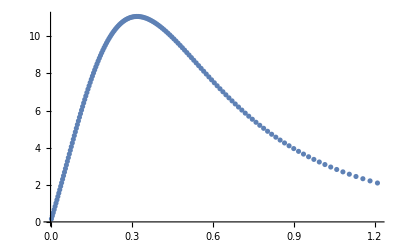

```mathematica
ListPlot[δFCurve[[;;,4;;5]]]
```

```mathematica
Isp=δFCurve[[Position[δFCurve[[;;,5]],Max[δFCurve[[;;,5]]]][[1]]]][[1]]
```

{1.52,0.93,1.22273,0.318801,11.066,0.835156}

```mathematica
SetDirectory[NotebookDirectory[]];
Save["dpCurveWithFriction",δFCurve]
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*Get["dpCurveWithFriction"];*)
Isp=δFCurve[[Position[δFCurve[[;;,5]],Max[δFCurve[[;;,5]]]][[1]]]][[1]]
```

{1.52,0.93,1.22273,0.318801,11.066,0.835156}

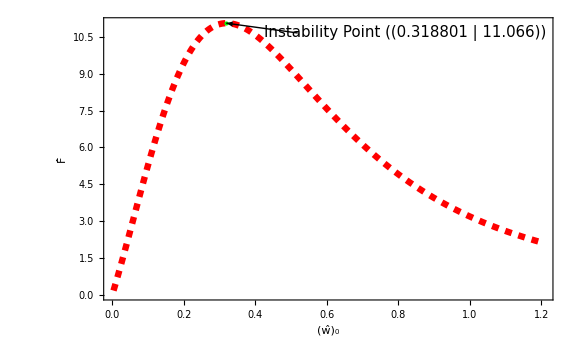

```mathematica
pIsp=Graphics[{PointSize[Large],Green,Point[Isp[[4;;5]]]}];
pArrow=Graphics[Arrow[{Isp[[4;;5]]+{0.2,-0.4},Isp[[4;;5]]}]];
ptext=Graphics[Text[Style["Instability Point "@{Isp[[4;;5]]},FontSize->15],Isp[[4;;5]]+{0.5,-0.4}]];
p1=ListPlot[δFCurve[[;;,4;;5]],Joined->True,PlotStyle->Directive[Red,Thickness[0.008],Dashed],PlotRange->Automatic,ImageSize->Large,GridLines->None,Ticks->Automatic,AxesStyle->Directive[Black,FontFamily->"Times",16],Frame->True,FrameStyle->Directive[FontFamily->"Times",12],FrameLabel->{Style["(ŵ)_0",Black,FontFamily->"Times",16],Style["F̂",Black,FontFamily->"Times",16]}];
Show[p1,pIsp,pArrow,ptext]
```

### Analytical solution

For the problem

θ''(s)+P̂ sin(θ(s))=0
θ(0)==0
θ(1)==0

For the current problem

(d^2 g(ξ))/(d ξ^2)+k (cos(g(ξ))-μ  sin(g(ξ)))=0
g(ξ=0)=0
g'(ξ=0)=0
g(ξ=1)=-θ_0

We can write it as equation of β(ξ)=g(ξ)+g_0, where sin(g_0)=1/(√(1+μ^2)),cos(g_0)=-μ/(√(1+μ^2))

(d^2 β(ξ))/(d ξ^2)+k √(1+μ^2) sin(β)=0
β(ξ=0)=g_0=arccos(-μ/(√(1+μ^2)))
β'(ξ=0)=0

```mathematica
PShape[P_]:=Reap@Module[{solk,kn,soly,solx},
solk =FindRoot[EllipticK[k]-Sqrt[P]/2,{k,0.1}];
kn =k/.solk;
θ[s_]=2ArcSin[Sqrt[kn] JacobiSN[s Sqrt[P]+EllipticK[kn],kn]];
(*solx =NDSolve[{x'[s]==Cos[θ[s]],x[0]==0},x[s],{s,0,1}];
soly= NDSolve[{y'[s]==Sin[θ[s]],y[0]==0},y[s],{s,0,1}];
*)
x[s_]=-s+2/Sqrt[P](EllipticE[JacobiAmplitude[s Sqrt[P]+EllipticK[kn],kn],kn]-EllipticE[JacobiAmplitude[EllipticK[kn],kn],kn]);
y[s_]=-2 Sqrt[kn]/Sqrt[P] JacobiCN[s Sqrt[P]+EllipticK[kn],kn];
dflection = y[s]/.s->1/2;
Sow[dflection];
ParametricPlot[{Chop[x[s],10^-6],y[s]},{s,0,1},PlotRange->All,PlotStyle->{Dashed},ImageSize->Large]
]
```